# Uncoupled Model

## Supporting Information Insights into chemically-fueled supramolecular polymers

Anastasiia Sharko, Dimitri Livitz, Serena De Piccoli1, Kyle J. M. Bishop, and Thomas M. Hermans

```mathematica
ClearAll[MPLColorMap]
<<"http://pastebin.com/raw/pFsb4ZBS";
bigSize = 14;
smallSize=12;
thin =0.6;
```

## Dynamical Regimes

### Model equations

ḟ=-k_a f(c_tot-m_1)
(ṁ)_1=k_a f(c_tot-m_1)-k'_d m_1 a 

with initial conditions f(0)=f_0 and m_1(0)=0.  Let k_a→1 and c_tot→1 such that concentrations are measured in units of c_tot and time in units of (k_a c_tot)^-1.

### Regime Map

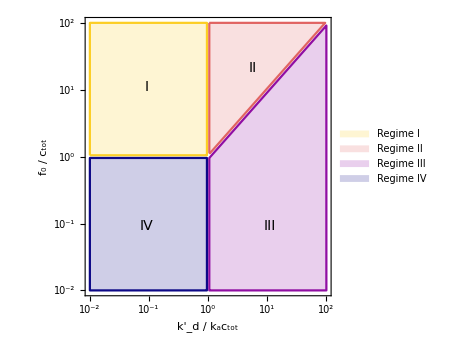

```mathematica
gap=0.02;
map=RegionPlot[{
{(f0>gap)&& (kd<-gap),
(f0>kd+ gap)&& (kd>gap),
(f0<kd-2gap)&& (kd>gap),
(f0<-gap)&& (kd<-gap)}},{kd,-2,2},{f0,-2,2},
Mesh->None,
PlotPoints->50,
PlotRange->{{-2,2},{-2,2}},
BoundaryStyle->{1->Lighter[MPLColorMap["Plasma"][0.9],0],2->Lighter[MPLColorMap["Plasma"][0.6],0],3->Lighter[MPLColorMap["Plasma"][0.3],0],
4->Lighter[MPLColorMap["Plasma"][0.0],0]},
PlotStyle->{Lighter[MPLColorMap["Plasma"][0.9],0.8],Lighter[MPLColorMap["Plasma"][0.6],0.8],Lighter[MPLColorMap["Plasma"][0.3],0.8],
Lighter[MPLColorMap["Plasma"][0.0],0.8]},
ImageSize->350,
ImagePadding->{{60,20},{60,20}},
PlotLegends->{"Regime I","Regime II","Regime III","Regime IV"},
LabelStyle->Directive[Black,FontSize->smallSize],
FrameStyle->Directive[Black,AbsoluteThickness[thin]],
FrameLabel->{Style["k'_d / k_ac_tot",bigSize],Style["f_0 / c_tot",bigSize]},
FrameTicks->{
{Table[{i,Superscript[10,i]},{i,-2,2}],
Table[{i,""},{i,-10,5,5}]},
{Table[{i,Superscript[10,i]},{i,-2,2}],
Table[{i,""},{i,-10,5,5}]}},
Epilog->{Text[Style["IV",bigSize],Scaled[{0.25,0.25}]],
Text[Style["III",bigSize],Scaled[{0.75,0.25}]],
Text[Style["I",bigSize],Scaled[{0.25,0.75}]],
Text[Style["II",bigSize],Scaled[{0.68,0.82}]]}]
```

```mathematica
(* Export[NotebookDirectory[]<>"figures/regime_map.pdf",map] *)
```

## Regime I: f_0≫1 and k'_d≪1

#### Figure 6 (regime I)

```mathematica
Clear[m1,f,kd,f0];
tmax=800;
param={kd->0.05,f0->20};
sol=NDSolve[{
f'[t]==- f[t] (1-m1[t]),
m1'[t]== f[t] (1-m1[t])-kd m1[t],
m1[0]==0,
f[0]==f0}/.param,{f[t],m1[t]},{t,0,tmax}];
```

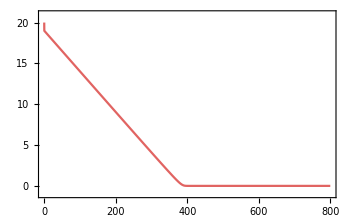
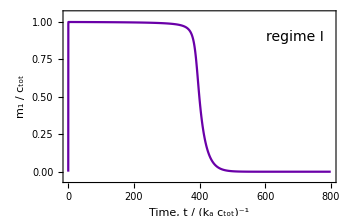

```mathematica
plot1=Plot[{m1[t]/.sol[[1]]},{t,0,tmax},
LabelStyle->Directive[Black,FontSize->smallSize],
FrameLabel->{
Style["Time, t / (k_a c_tot)^-1 ",FontSize->bigSize],
Style["m_1 / c_tot",FontSize->bigSize]},
PlotRange->{-0.05,1.05},
PlotStyle->{Directive[MPLColorMap["Plasma"][0.2]]},
ImageSize->350,
AspectRatio->1/GoldenRatio,
ImagePadding->{{50,50},{50,25}},
Frame->{True,True,True,False},
FrameStyle->{
Directive[Black,AbsoluteThickness[thin]],
Directive[MPLColorMap["Plasma"][0.2],AbsoluteThickness[thin]],
Directive[Black,AbsoluteThickness[thin]],
Directive[Black,AbsoluteThickness[thin]]},
Epilog->{Text[Style["regime I",bigSize],Scaled[{0.85,0.85}]]}];
plot2=Plot[{f[t]/.sol[[1]]},{t,0,tmax},
PlotStyle->{Directive[MPLColorMap["Plasma"][0.6]]},
LabelStyle->Directive[Black,FontSize->smallSize],
FrameLabel->{{None,Rotate[Style["Fuel, f / c_tot",FontSize->bigSize],180 Degree]},{None,None}},
PlotRange->{-0.05,1.05}(f0/.param),
ImageSize->350,
AspectRatio->1/GoldenRatio,
ImagePadding->{{50,50},{50,25}},
Axes->False,
Frame->{False,False,False,True},
FrameTicks->{{None,All},{None,None}},FrameStyle->{
Directive[Black,AbsoluteThickness[thin]],
Directive[Black,AbsoluteThickness[thin]],
Directive[Black,AbsoluteThickness[thin]],
Directive[MPLColorMap["Plasma"][0.6],AbsoluteThickness[thin]]}];

region1=Overlay[{plot2,plot1}]
```

```mathematica
(* Export[NotebookDirectory[]<>"figures/regime1_plot.pdf", region1] *)
```

## Regime II: f_0≫k'_d and k'_d≫1

#### Figure 6 (regime II)

```mathematica
Clear[m1,f,kd,f0];
param={kd->20,f0->400};
tmax=2f0/kd/.param;
sol=NDSolve[{
f'[t]==- f[t] (1-m1[t]),
m1'[t]== f[t] (1-m1[t])-kd m1[t],
m1[0]==0,
f[0]==f0}/.param,{f[t],m1[t]},{t,0,tmax}];
```

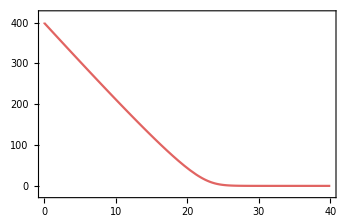
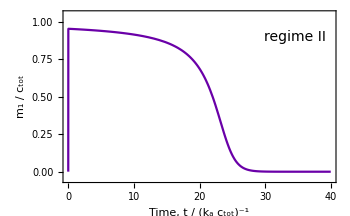

```mathematica
plot1=Plot[{m1[t]/.sol[[1]]},{t,0,tmax},
LabelStyle->Directive[Black,FontSize->smallSize],
FrameLabel->{
Style["Time, t / (k_a c_tot)^-1 ",FontSize->bigSize],
Style["m_1 / c_tot",FontSize->bigSize]},
PlotRange->{-0.05,1.05},
PlotStyle->{Directive[MPLColorMap["Plasma"][0.2]]},
ImageSize->350,
AspectRatio->1/GoldenRatio,
ImagePadding->{{50,50},{50,25}},
AspectRatio->1/GoldenRatio,
ImagePadding->{{50,50},{50,25}},
Frame->{True,True,True,False},
FrameStyle->{
Directive[Black,AbsoluteThickness[thin]],
Directive[MPLColorMap["Plasma"][0.2],AbsoluteThickness[thin]],
Directive[Black,AbsoluteThickness[thin]],
Directive[Black,AbsoluteThickness[thin]]},
Epilog->{Text[Style["regime II",bigSize],Scaled[{0.85,0.85}]]}];
plot2=Plot[{f[t]/.sol[[1]]},{t,0,tmax},
PlotStyle->{Directive[MPLColorMap["Plasma"][0.6]]},
LabelStyle->Directive[Black,FontSize->smallSize],
FrameLabel->{{None,Rotate[Style["Fuel, f / c_tot",FontSize->bigSize],180 Degree]},{None,None}},
PlotRange->{-0.05,1.05}(f0/.param),
ImageSize->350,
AspectRatio->1/GoldenRatio,
ImageSize->350,
AspectRatio->1/GoldenRatio,
ImagePadding->{{50,50},{50,25}},
Axes->False,
Frame->{False,False,False,True},
FrameTicks->{{None,All},{None,None}},FrameStyle->{
Directive[Black,AbsoluteThickness[thin]],
Directive[Black,AbsoluteThickness[thin]],
Directive[Black,AbsoluteThickness[thin]],
Directive[MPLColorMap["Plasma"][0.6],AbsoluteThickness[thin]]}];

region2=Overlay[{plot2,plot1}]
```

```mathematica
(* Export[NotebookDirectory[]<>"figures/regime2_plot.pdf",region2] *)
```

## Regime III: f_0≪k'_d and k'_d≫1

#### Figure 6 (regime III)

```mathematica
Clear[m1,f,kd,f0];
tmax=10;
param={kd->20,f0->1};
sol=NDSolve[{
f'[t]==- f[t] (1-m1[t]),
m1'[t]== f[t] (1-m1[t])-kd m1[t],
m1[0]==0,
f[0]==f0}/.param,{f[t],m1[t]},{t,0,tmax}];
```

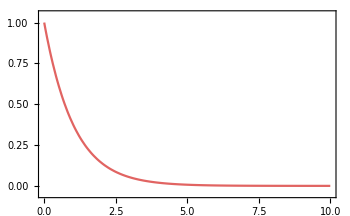
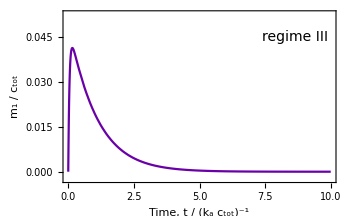

```mathematica
plot1=Plot[{m1[t]/.sol[[1]]},{t,0,tmax},
LabelStyle->Directive[Black,FontSize->smallSize],
FrameLabel->{
Style["Time, t / (k_a c_tot)^-1 ",FontSize->bigSize],
Style["m_1  / c_tot",FontSize->bigSize]},
PlotRange->{-0.05,1.05}(f0/kd/.param),
PlotStyle->{Directive[MPLColorMap["Plasma"][0.2]]},
ImageSize->350,
AspectRatio->1/GoldenRatio,
ImagePadding->{{50,50},{50,25}},
Frame->{True,True,True,False},
FrameStyle->{
Directive[Black,AbsoluteThickness[thin]],
Directive[MPLColorMap["Plasma"][0.2],AbsoluteThickness[thin]],
Directive[Black,AbsoluteThickness[thin]],
Directive[Black,AbsoluteThickness[thin]]},
Epilog->{Text[Style["regime III",bigSize],Scaled[{0.85,0.85}]]}];
plot2=Plot[{f[t]/.sol[[1]]},{t,0,tmax},
PlotStyle->{Directive[MPLColorMap["Plasma"][0.6]]},
LabelStyle->Directive[Black,FontSize->smallSize],
FrameLabel->{{None,Rotate[Style["Fuel, f / c_tot",FontSize->bigSize],180 Degree]},{None,None}},
PlotRange->{-0.05,1.05}(f0/.param),
ImageSize->350,
AspectRatio->1/GoldenRatio,
ImagePadding->{{50,50},{50,25}},
Axes->False,
Frame->{False,False,False,True},
FrameTicks->{{None,All},{None,None}},FrameStyle->{
Directive[Black,AbsoluteThickness[thin]],
Directive[Black,AbsoluteThickness[thin]],
Directive[Black,AbsoluteThickness[thin]],
Directive[MPLColorMap["Plasma"][0.6],AbsoluteThickness[thin]]}];

region3=Overlay[{plot2,plot1}]
```

```mathematica
(* Export[NotebookDirectory[]<>"figures/regime3_plot.pdf", region3] *)
```

## Regime IV: f_0≪1 and k'_d≪1

#### Figure 6 (regime IV)

```mathematica
Clear[m1,f,kd,f0];
tmax=100;
param={kd->0.05,f0->0.05};
sol=NDSolve[{
f'[t]==- f[t] (1-m1[t]),
m1'[t]== f[t] (1-m1[t])-kd m1[t],
m1[0]==0,
f[0]==f0}/.param,{f[t],m1[t]},{t,0,tmax}];
```

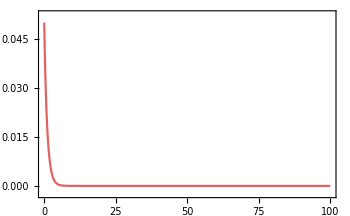
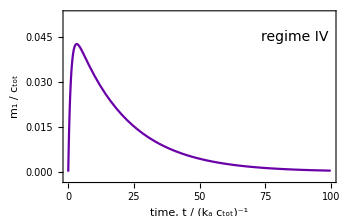

```mathematica
plot1=Plot[{m1[t]/.sol[[1]]},{t,0,tmax},
LabelStyle->Directive[Black,FontSize->smallSize],
FrameLabel->{
Style["time, t / (k_a c_tot)^-1 ",FontSize->bigSize],
Style["m_1 / c_tot",FontSize->bigSize]},
PlotRange->{-0.05,1.05}(f0/.param),
PlotStyle->{Directive[MPLColorMap["Plasma"][0.2]]},
ImageSize->350,
AspectRatio->1/GoldenRatio,
ImagePadding->{{50,50},{50,25}},
Frame->{True,True,True,False},
FrameStyle->{
Directive[Black,AbsoluteThickness[thin]],
Directive[MPLColorMap["Plasma"][0.2],AbsoluteThickness[thin]],
Directive[Black,AbsoluteThickness[thin]],
Directive[Black,AbsoluteThickness[thin]]},
Epilog->{Text[Style["regime IV",bigSize],Scaled[{0.85,0.85}]]}];
plot2=Plot[{f[t]/.sol[[1]]},{t,0,tmax},
PlotStyle->{Directive[MPLColorMap["Plasma"][0.6]]},
LabelStyle->Directive[Black,FontSize->smallSize],
FrameLabel->{{None,Rotate[Style["Fuel, f / c_tot",FontSize->bigSize],180 Degree]},{None,None}},
PlotRange->{-0.05,1.05}(f0/.param),
ImageSize->350,
AspectRatio->1/GoldenRatio,
ImagePadding->{{50,50},{50,25}},
Axes->False,
Frame->{False,False,False,True},
FrameTicks->{{None,All},{None,None}},FrameStyle->{
Directive[Black,AbsoluteThickness[thin]],
Directive[Black,AbsoluteThickness[thin]],
Directive[Black,AbsoluteThickness[thin]],
Directive[MPLColorMap["Plasma"][0.6],AbsoluteThickness[thin]]}];

region4=Overlay[{plot2,plot1}]
```

```mathematica
(*Export[NotebookDirectory[]<>"figures/regime4_plot.pdf",region4]*)
```

#### Compared with approximation

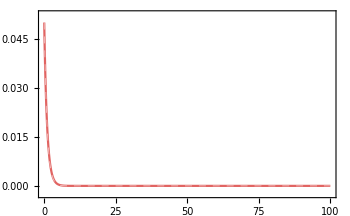
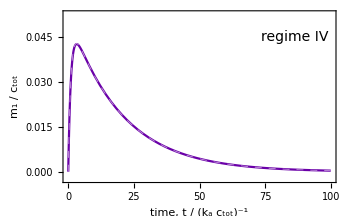

```mathematica
plot1=Plot[{a[t]/.sol[[1]],f0/(kd-1)(ⅇ^-t-ⅇ^(-kd t))/.param},{t,0,tmax},
LabelStyle->Directive[Black,FontSize->smallSize],
FrameLabel->{
Style["time, t / (k_a c_tot)^-1 ",FontSize->bigSize],
Style["m_1 / c_tot",FontSize->bigSize]},
PlotRange->{-0.05,1.05}(f0/.param),
PlotStyle->{Directive[MPLColorMap["Plasma"][0.2]],Directive[Lighter[MPLColorMap["Plasma"][0.2],0.6],Dashed,AbsoluteThickness[thin]]},
ImageSize->350,
AspectRatio->1/GoldenRatio,
ImagePadding->{{50,50},{50,25}},
Frame->{True,True,True,False},
FrameStyle->{
Directive[Black,AbsoluteThickness[thin]],
Directive[MPLColorMap["Plasma"][0.2],AbsoluteThickness[thin]],
Directive[Black,AbsoluteThickness[thin]],
Directive[Black,AbsoluteThickness[thin]]},
Epilog->{Text[Style["regime IV",bigSize],Scaled[{0.85,0.85}]]}];
plot2=Plot[{f[t]/.sol[[1]],f0 ⅇ^-t /.param},{t,0,tmax},
PlotStyle->{Directive[MPLColorMap["Plasma"][0.6]],
Directive[Lighter[MPLColorMap["Plasma"][0.6],0.6],Dashed,AbsoluteThickness[thin]]},
LabelStyle->Directive[Black,FontSize->smallSize],
FrameLabel->{{None,Rotate[Style["Fuel, f / c_tot",FontSize->bigSize],180 Degree]},{None,None}},
PlotRange->{-0.05,1.05}(f0/.param),
ImageSize->350,
AspectRatio->1/GoldenRatio,
ImagePadding->{{50,50},{50,25}},
Axes->False,
Frame->{False,False,False,True},
FrameTicks->{{None,All},{None,None}},FrameStyle->{
Directive[Black,AbsoluteThickness[thin]],
Directive[Black,AbsoluteThickness[thin]],
Directive[Black,AbsoluteThickness[thin]],
Directive[MPLColorMap["Plasma"][0.6],AbsoluteThickness[thin]]}];

Overlay[{plot2,plot1}]
```

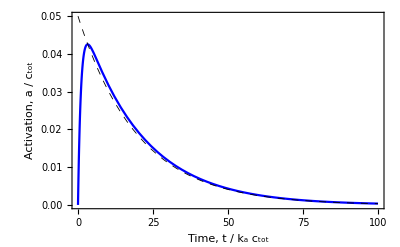

```mathematica
Plot[{a[t]/.sol[[1]],f0 Exp[-kd t]/.param},{t,0,tmax},PlotRange->Full,
LabelStyle->Directive[Black,FontSize->smallSize],
PlotStyle->{Blue,Directive[Black,Dashed,AbsoluteThickness[thin]]},
Frame->True,
PlotStyle->{Automatic,Dashed},
FrameLabel->{Style["Time, t / k_a c_tot",FontSize->bigSize],Style["Activation, a / c_tot",FontSize->bigSize]}]
```

## Figure 6

```mathematica
grid=Style[Grid[{{region1,region2},{region4,region3}}],ImageSizeMultipliers->{1,1}]
```

-Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics-

```mathematica
(* Export[NotebookDirectory[]<>"figures/regime_plot.pdf",grid] *)
```

/Users/kjmbishop/Dropbox (Bishop Group)/Research/ChemRev/Review 2020/_REVISIONS/figures/regime_plot.pdf